```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dan/ResearchLocal/tools"];
```

## Cos temp profile setup

```mathematica
nz=8*10;
```

```mathematica
Tatm0=40;Tmid0=19;zq0=2.0;q=1.0;r=115;
```

```mathematica
Tmid=Tmid0(r/200)^-0.5
Tatm=Tatm0(r/155)^-0.3
zq=63(r/200)^1.3*Exp[-(r/800)^2]
δ=0.0034(r/1-200)+2.5
```

43.7472

25.0565

30.0562

2.211

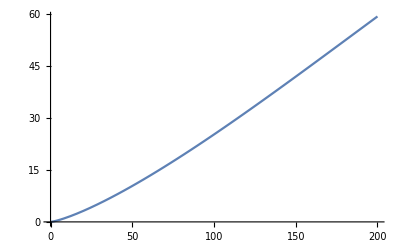

```mathematica
Plot[63(r/200)^1.3*Exp[-(r/800)^2],{r,0,200}]
```

```mathematica
TcosTemp[z_]:=If[Abs[z]<zq,Tatm+(Tmid-Tatm)(Cos[(π z)/(2zq)])^(2δ),Tatm];
```

```mathematica
tempNormFactor=Mean[Table[TcosTemp[z],{z,-4,4,0.1}]]*2;
```

```mathematica
Tmid/tempNormFactor
Tatm/tempNormFactor
zq
δ
```

0.488274

0.8525

30.0562

2.211

```mathematica
Tcos[z_]:=TcosTemp[z]/tempNormFactor
```

```mathematica
z=Table[(i-0.5)/(nz/8)//N,{i,1,nz/2}];
```

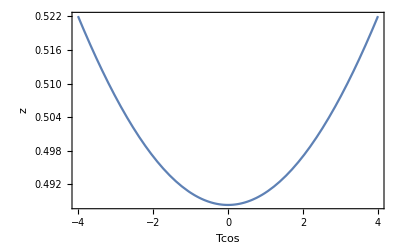

```mathematica
Plot[Tcos[z],{z,-4,4},PlotRange->Full,Frame->True,FrameLabel->{"Tcos","z"}]
```

```mathematica
P0=0.5;
sCos=NDSolve[{1/ρ1[z1] D[(Tcos[z1]*ρ1[z1]), z1]==-z1,ρ1[0]==P0/Tcos[0]},ρ1[z1],{z1,0,4}];
ρCos[z1_]:=Evaluate[ρ1[z1]/.sCos];
Pcos[z1_]:=ρCos[z1]*Tcos[z1]
ρCosTab=Table[ρCos[z1][[1]],{z1,z}];
```

```mathematica
ρmid=1;
ρIsoTab=Table[ρmid*Exp[-z[[i]]^2],{i,1,nz/2}];
```

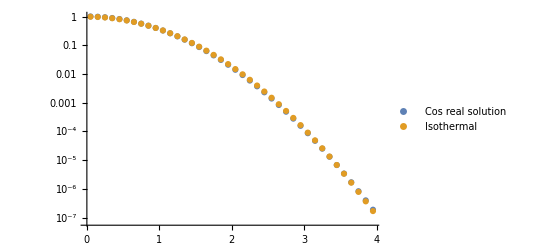

```mathematica
ListLogPlot[{Transpose[{z,ρCosTab}],Transpose[{z,ρIsoTab}]},PlotRange->Full,PlotLegends->{"Cos real solution","Isothermal"},PlotRange->Full]
```

```mathematica
ks=4; ke=43; nghost=4;
stringArray=Table[StringJoin["pGrid->U[",ToString[k],"][js-1][is-1].d = ",ToString[AccountingForm[ρCosTab[[k-(ke+nghost+1)/2+1]]]],"; \n"],{k,(ke+1+nghost)/2,ke}];
StringJoin[stringArray]
```

```mathematica
"pGrid->U[24][js-1][is-1].d = 1.01682; \npGrid->U[25][js-1][is-1].d = 0.996115; \npGrid->U[26][js-1][is-1].d = 0.955973; \npGrid->U[27][js-1][is-1].d = 0.898786; \npGrid->U[28][js-1][is-1].d = 0.827843; \npGrid->U[29][js-1][i\n"
```

```mathematica
(*P0=0.5;
ρmid=P0/Tmid;
δz=8/nz//N
T=Table[Tcos[z1],{z1,z}];
ρ=Table[0,{i,1,nz/2}];
ρ[[1]]=ρmid;
Do[ρ[[i]]=ρ[[i-1]]*(2-(z[[i-1]] δz)/T[[i-1]]-T[[i]]/T[[i-1]]),{i,2,nz/2}]
P=ρ*T;*)
```